# Degree of Polarisation for the Barrel Detector

In this file you can calculate the degree of polarisation for the big barrel detector. Huge chunks of code are taken from the ‘Degree of Polarisation’ and the ‘Degree of Polarisation Batch Processing’ notebooks.

```mathematica
Needs["ErrorBarPlots`"]
```

## Data Import

Importing the data.

```mathematica
files=FileNames["*-degree-of-polarisation*.dat",NotebookDirectory[]] 
data=Import[#]&/@files;
```

{C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-22-1100-degree-of-polarisation.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-22-1125-degree-of-polarisation.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-22-1200-degree-of-polarisation.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-22-1340-degree-of-polarisation.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-22-1500-degree-of-polarisation.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-23-1325-degree-of-polarisation.dat}

Specifying a position file to take the positions from. Only one at a time possible. So if measurement required a new position file it also needs a new notebook like this one you are reading right now.

```mathematica
position= Import[NotebookDirectory[]<>"2018-11-22-1500-degree-of-polarisation.position","Table"]  [[1]][[;;;;4]];
```

## Definitions

## Data Cleaning & Error Calculation

```mathematica
countsPencilNormalized=Transpose[#[[5;;-1]]][[5]]&/@data;
countsPencil=Transpose[#[[5;;-1]]][[2]]&/@data;
```

Calculating the actual counts of the barrel detector. cts_barrel = norm_barrel * cts_pencil.

```mathematica
counts=countsPencil[[#]]/countsPencilNormalized[[#]]&/@Range[Length[countsPencil]]
```

{{43.,23.,20.,35.,62.,49.,34.,48.,58.,39.,45.,75.,69.,79.,58.,79.},{40.,26.,30.,30.,58.,37.,33.,48.,63.,42.,41.,60.,83.,51.,51.,64.},{31.,29.,23.,32.,33.,26.,18.,47.,22.,26.,25.,34.,34.,28.,29.,30.},{43.,37.,41.,35.,35.,35.,36.,28.,30.,27.,28.,34.,23.,32.,26.,30.},{34.,27.,30.,40.,15.,35.,29.,27.,23.,26.,31.,26.,36.,31.,29.,15.,27.,26.,26.,33.,65.,41.,35.,51.,64.,51.,53.,55.,73.,48.,53.,65.,59.,46.,73.,63.},{38.,24.,29.,33.,24.,24.,33.,20.,27.,27.,20.,27.,23.,30.,24.,25.,30.,20.,27.,25.,24.,18.,25.,24.,23.,32.,20.,30.,21.,24.,30.,23.,25.,28.,17.,31.,23.,19.,27.,27.,26.,25.,30.,35.,23.,12.,17.,40.,26.,22.,30.,28.,30.,29.,26.,47.,45.,31.,32.,45.,66.,31.,29.,45.,55.,43.,40.,45.,65.,37.,40.,60.,51.,16.,50.,51.,60.,54.,55.,47.,63.,53.,51.,61.,59.,63.,63.,64.,69.,63.,57.,61.,64.,58.,52.,68.,68.,57.,63.,62.}}

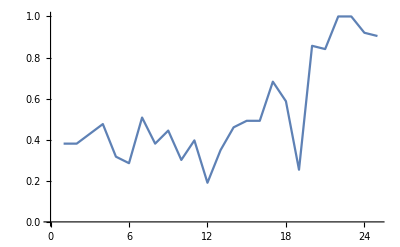

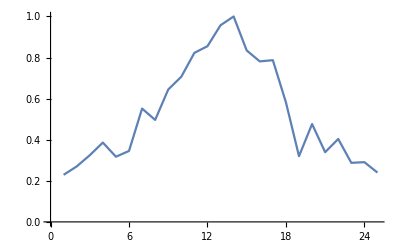

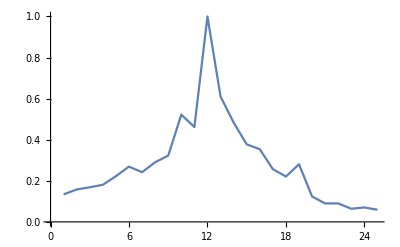

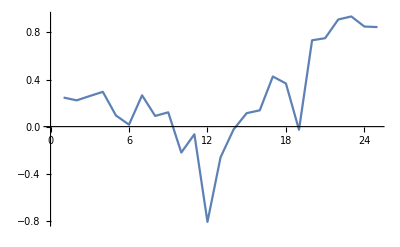

```mathematica
a=counts[[6]][[2;;;;4]];
b=countsPencil[[6]][[2;;;;4]];
c=countsPencilNormalized[[6]][[2;;;;4]];
a=a/Max[a];
b=b/Max[b];
c=c/Max[c];
ListLinePlot[a]
ListLinePlot[b]
ListLinePlot[c]
ListLinePlot[a-c]
```